```mathematica
F=9×10^-5;
```

```mathematica
θ=4.6 ×10^-3;
```

```mathematica
ts=0.5;
```

```mathematica
γ=-0.0044;
```

```mathematica
H0=3×10^-5;
```

```mathematica
ti=ts/2-√(1/(2F)+ts^2/4);
```

```mathematica
tf=ts/2+√(1/(2F)+ts^2/4);
```

```mathematica
a=(-2γ)^(1/3)/θ;
```

```mathematica
W[φ_]=Exp[F/θ^2(Log[φ/a]-θ ts)^2];
```

```mathematica
Ω[φ_]=W[φ] θ^3 (θ φ)^3+H0(4 F Log[φ/a]^2-4θ ts F Log[φ/a]+2θ (θ φ)^3 Log[φ/a]-2 θ^2);
```

```mathematica
k[φ_]=-(12 Log[φ/a]^2 H0^2-3W[φ](Ω[φ]-H0 θ(θ φ)^3 Log[φ/a]))/(W[φ]^2 θ^2(θ φ)^2);
```

```mathematica
q[φ_]=(12 Log[φ/a]^2 H0^2-2W[φ](Ω[φ]+H0 θ(θ φ)^3 Log[φ/a]))/(W[φ]^2 θ^2(θ φ)^4);
```

```mathematica
DK[φ_]=D[k[φ], φ];
```

```mathematica
DQ[φ_]=D[q[φ], φ];
```

```mathematica
ddφminus[φ_, y_]=-(2DK[φ] y^2+3DQ[φ] y^4+3q[φ] y^6+12(y^4/2-y √(y^6/4+(k[φ] y^2)/6+(q[φ] y^4)/4))(k[φ]+q[φ] y^2+3/2 y^4))/(4(k[φ]+3q[φ] y^2-6y √(y^6/4+(k[φ] y^2)/6+(q[φ] y^4)/4)+9/2 y^4));
```

```mathematica
cs2minus[φ_, y_]=(k[φ]+q[φ] y^2+2ddφminus[φ,y]+4y(y^3/2-√(y^6/4+(k[φ] y^2)/6+(q[φ] y^4)/4))-y^4/2)/(k[φ]+3q[φ] y^2+6y(y^3/2-√(y^6/4+(k[φ] y^2)/6+(q[φ] y^4)/4))+(3 y^4)/2);
```

```mathematica
B[φ_, y_]=k[φ]+q[φ] y^2+2ddφminus[φ,y]+4.0y(y^3/2.0-√(y^6/4.0+(k[φ] y^2)/6.0+(q[φ] y^4)/4.0))-y^4/2.0;
```

```mathematica
A[φ_, y_]=k[φ]+3q[φ] y^2+6y(y^3/2-√(y^6/4+(k[φ] y^2)/6+(q[φ] y^4)/4))+(3 y^4)/2;
```

```mathematica
Hdot[φ_, y_]=(-0.5*k[φ]-0.5*q[φ] y^2+0.5*ddφminus[φ,y]-1.5*y(y^3/2.0-√(y^6/4.0+(k[φ] y^2)/6.0+(q[φ] y^4)/4.0)));
```

Greater::nord: Invalid comparison with -0.000314424+0.0000528495 ⅈ attempted.

Greater::nord: Invalid comparison with 10.1132-1.88402 ⅈ attempted.

Greater::nord: Invalid comparison with -0.000196129-0.0000187193 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Less::nord: Invalid comparison with -1696.82+1860.42 ⅈ attempted.

Less::nord: Invalid comparison with -641.354+1749.88 ⅈ attempted.

Less::nord: Invalid comparison with -66.7419+1547.25 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

Less::nord: Invalid comparison with 0.0416167-0.0183719 ⅈ attempted.

Less::nord: Invalid comparison with 0.0346764-0.024227 ⅈ attempted.

Less::nord: Invalid comparison with 0.0298875-0.0286322 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

Less::nord: Invalid comparison with -0.000018237-0.0000239229 ⅈ attempted.

Less::nord: Invalid comparison with -0.0000150086-0.0000291139 ⅈ attempted.

Less::nord: Invalid comparison with -9.18562×10^-6-0.0000336435 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with 10.1132-1.88402 ⅈ attempted.

Greater::nord: Invalid comparison with 18.7563-5.89812 ⅈ attempted.

Greater::nord: Invalid comparison with 37.5514-21.3089 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

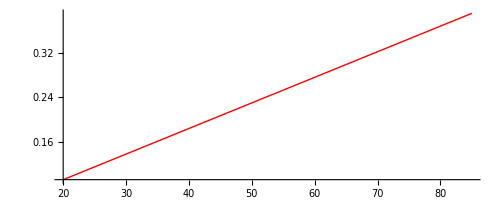

```mathematica
SetOptions[RegionPlot,{FrameLabel->{ϕ, ϕ̇},BaseStyle->{FontSize->19}},PerformanceGoal->"Quality",PlotPoints->100];

NEC=RegionPlot[{Hdot[φ, y]>0.0  && cs2minus[φ, y]>0.0 && A[φ, y]>0.0 && y^6/4.0+(k[φ] y^2)/6.0+(q[φ] y^4)/4.0>0 },  {φ,20, 85}, {y, 0, 0.4},PlotStyle->{LightBlue,Opacity[0.9]},BoundaryStyle->Dashed];

cssm0=RegionPlot[{cs2minus[φ, y]<0.0 },  {φ,20, 85}, {y, 0, 0.4},PlotStyle->{LightOrange,Opacity[1.0]}];

GradInst = RegionPlot[{B[φ, y]<0.0},{φ,20, 85}, {y, 0, 0.4},PlotStyle->{Brown,Opacity[1.0]}];

Ghost=RegionPlot[{A[φ, y]<0.0 },  {φ,20, 85}, {y, 0, 0.4},PlotStyle->{Orange,Opacity[1.0]}];


csg1=RegionPlot[{cs2minus[φ, y]>1.0 },  {φ,20, 85}, {y, 0, 0.4},PlotStyle->{Red,Opacity[0.5]}];

dyninacc = RegionPlot[{y^6/4.0+(k[φ] y^2)/6.0+(q[φ] y^4)/4.0<0.0},{φ,20, 85}, {y, 0, 0.4},PlotStyle->{Yellow,Opacity[1.0]}];
Traj = ParametricPlot[{φ,θ*φ},{φ,20, 85},PlotStyle->{Red,Thick}]
```

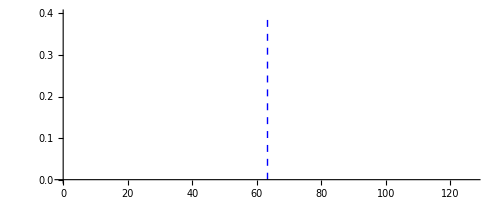

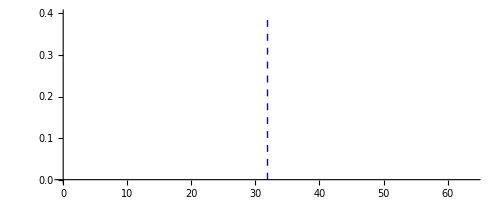

```mathematica
Bound2 = ParametricPlot[{63.3102,y},{y,0, 0.4},PlotStyle->{Blue,Thick, Dashed}]
Bound1 = ParametricPlot[{31.8907,y},{y,0, 0.4},PlotStyle->{Blue,Thick, Dashed}]
```

```mathematica
Hplot=ContourPlot[y^3/2.0-√(y^6/4.0+(k[φ] y^2)/6.0+(q[φ] y^4)/4.0)==0.0,{φ,20,85},{y,0,0.4},ContourStyle->{Black,Dashed, Thick}];
```

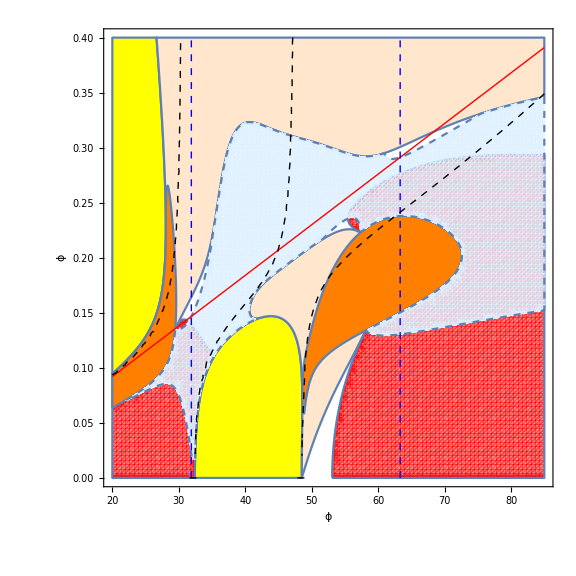

```mathematica
Show[dyninacc,csg1,cssm0,Ghost, NEC, Traj, Bound1, Bound2, Hplot, ImageSize->Large]
```

```mathematica
Export["/Users/joseg/Desktop/Bouncing/PS2.pdf",%642,"PDF"]
```

/Users/joseg/Desktop/Bouncing/PS2.pdf

```mathematica
Export["/Users/joseg/Desktop/Bouncing/PS2.pdf",%640,"PDF"]
```

/Users/joseg/Desktop/Bouncing/PS2.pdf

```mathematica
Export["/Users/joseg/Desktop/Bouncing/PS2.pdf",%635,"PDF"]
```

/Users/joseg/Desktop/Bouncing/PS2.pdf